## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\Growth\\git\\CoChiSquare"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_]=H0 √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

## CAL

### Plot SN data with error bar

#### Import and display “SCPUnion2_AllSNe.tex”

Read the data file of SCPUnion2_mu_vs_z.txt

```mathematica
dataunionfulltmp=Import["DATA\\UNION2\\SCPUnion2_AllSNe.tex","Table"];
```

Import::nffil: File not found during Import.

Length of dataunionfulltmp

```mathematica
lenfull=Length[dataunionfulltmp];
```

Delete the & simbols in dataunionfulltmp

```mathematica
dataunionfull=Table[{dataunionfulltmp[[i,1]],dataunionfulltmp[[i,3]],dataunionfulltmp[[i,5]],dataunionfulltmp[[i,7]],dataunionfulltmp[[i,9]],dataunionfulltmp[[i,11]],dataunionfulltmp[[i,13]],dataunionfulltmp[[i,15]]},{i,1,lenfull}];
dataunionfulltable=Grid[Join[{{Name,Redshift,Mag,Stetch,Color,Distance,Sample,CutsFails}},dataunionfull], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

Table::iterb: Iterator {i, 1, lenfull} does not have appropriate bounds.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

#### Import and display “SCPUnion2_mu _vs _z _adjust.txt”

Import dataunion adjusted data. This data includes name, redshift, distance, error.

```mathematica
dataunion=Import["DATA\\UNION2\\SCPUnion2_mu_vs_z_adjust.txt","Table"];
datauniontable=Grid[Join[{{Name,Redshift,Distance,Error}},dataunion], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{LightGray,None}}];
```

Show dataunion table.

```mathematica
datauniontable;
```

Length of this dataunion table

```mathematica
len=Length[dataunion];
```

Simplify dataunion table and call it du

```mathematica
du=Table[{dataunion[[i,2]],dataunion[[i,3]],dataunion[[i,4]]},{i,1,len}];
dutable=Grid[Join[{{Redshift,Distance,Error}},du], Alignment -> Left, Spacings -> {2, 1}, Frame -> All,ItemStyle->"Text", Background->{{Gray,None},{None,None}}];
```

Show du table

```mathematica
dutable;
```

#### Visualize data.

Plot du table. That is SN

```mathematica
plunion=ErrorListPlot[du,PlotRange->All];
```

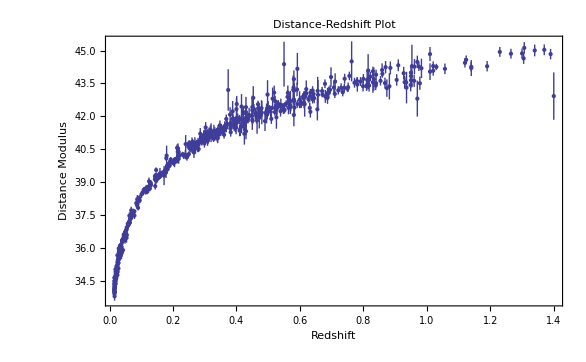

```mathematica
Show[plunion,Frame->True,FrameLabel->{"Redshift","Distance Modulus"},PlotLabel->Style["Distance-Redshift Plot",16,Orange]]
```

### Transition redshift, deceleration parameter, theoretically.

#### Theoretical Function and Values of distance/mag at different redshift.

Distance at redshift z

```mathematica
dz[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=(1+z)NIntegrate[1/hubble[Ωm0,Ωd0,Ωk0,tmp],{tmp,0,z}];
```

Magnitude calculated from distance. Theoretically of cause.

```mathematica
mag[Ωm0_?NumberQ,Ωd0_?NumberQ,Ωk0_?NumberQ,z_?NumberQ]:=5Log[10,c*dz[Ωm0,Ωd0,Ωk0,z]]+25;
```

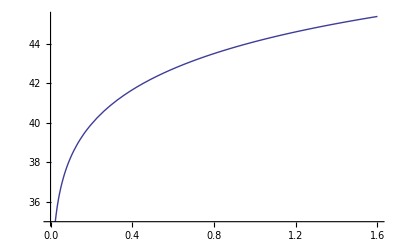

```mathematica
plmagth=Plot[mag[Ωm0w,Ωd0w,0,z],{z,0,1.6}]
```

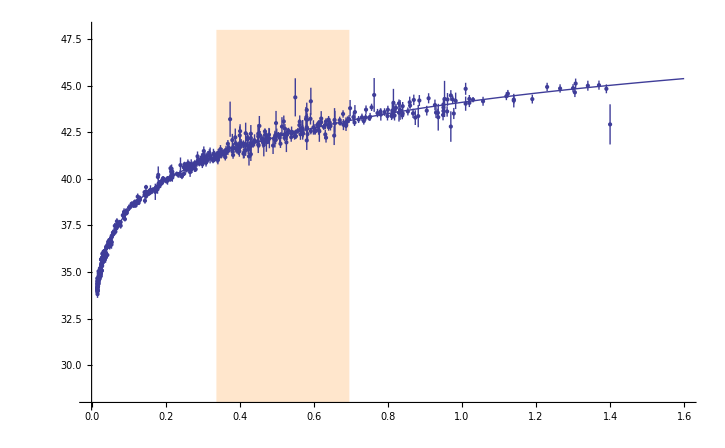

```mathematica
Show[{plunion,plmagth},PlotRange->{{0,1.6},{28,48}},AxesOrigin->{0,28},Prolog->{LightOrange,Rectangle[{0.426-0.089,28},{0.426+0.27,48}]}]
```

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,5},PlotRange->{{-1.05,5},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0}]
```

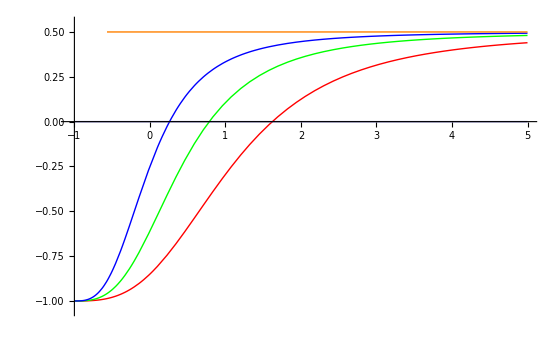

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1}]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

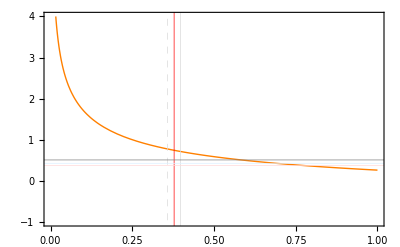

```mathematica
pldecr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

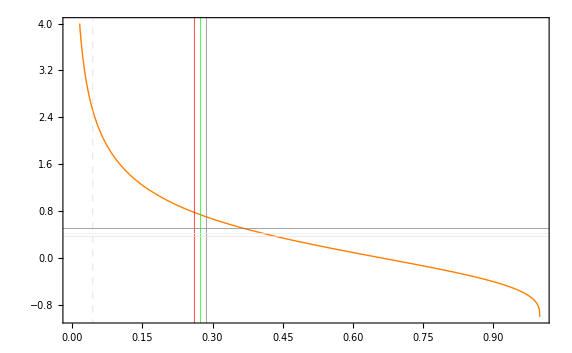

```mathematica
pldecr=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

### chi square fitting. Using mathematica’s functions.

#### Definations etc

chi square defination with error only.

```mathematica
chi2unionsl[Ωm0_?NumberQ,zt_?NumberQ]:=ParallelSum[(du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]])^2/du[[i,3]]^2,{i,1,len}]
```

Define a vector/table of  “theory-observation”.

```mathematica
thobtab[Ωm0_,zt_]=ParallelTable[du[[i,2]]-mag[Ωm0,1/2 Ωm0(1+zt)^3,1-Ωm0-1/2 Ωm0(1+zt)^3,du[[i,1]]],{i,1,len}];
```

Import covariance matrix data. “covm” is data with systematic and “covmns” is data without sys.

```mathematica
covm=Import["DATA/UNION2/SCPUnion2_covmat_sys.txt","Table"];
icovm=Inverse[covm];
```

```mathematica
covmns=Import["DATA/UNION2/SCPUnion2_covmat_nosys.txt","Table"];
icovmns=Inverse[covmns];
```

Testing the imported file.

```mathematica
(du[[1]][[3]])^-2
icovmns[[1,1]]
```

19.5538

19.5535

Define chi2 with and without systematic.

```mathematica
chi2union[Ωm0_?NumberQ,zt_?NumberQ]:=thobtab[Ωm0,zt].icovm.thobtab[Ωm0,zt]
```

```mathematica
chi2unionns[Ωm0_?NumberQ,zt_?NumberQ]:=thobtab[Ωm0,zt].icovmns.thobtab[Ωm0,zt]
```

Test the calcuation speed.

```mathematica
chi2union[0.27,0.5]//Timing
```

{8.236,560.12}

```mathematica
chi2unionns[0.27,0.5]//Timing
```

{8.128,735.117}

```mathematica
chi2unionsl[0.27,0.5]//Timing
```

NIntegrate::nlim: tmp = z is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.156,735.121}

#### Find the minimum chi2 for chi2 def. without sys.. AND Export the results to folder DATA/2/

```mathematica
Off[FindMinimum::lstol]
chi2minins=FindMinimum[chi2unionns[x,y],{x,0.15},{y,0.4}]
On[FindMinimum::lstol]
```

{546.166,{x→0.587724,y→0.533675}}

```mathematica
Export["OUTPUT\\2\\chi2unionns_minimum.dat",chi2minins]
```

OUTPUT\2\chi2unionns_minimum.dat

```mathematica
(* chi2minins={546.1663550716052,{x->0.5877241605370803,y->0.5336749032665581}} *)(*Should import what have been exported.*)
```

{546.166,{x→0.587724,y→0.533675}}

Without sys.

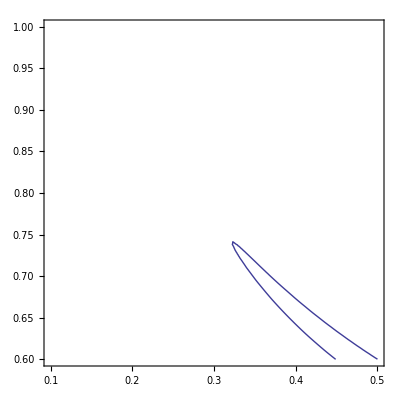

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2ns1s=ContourPlot[{chi2unionns[Ωm0,zt]==chi2minins[[1]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

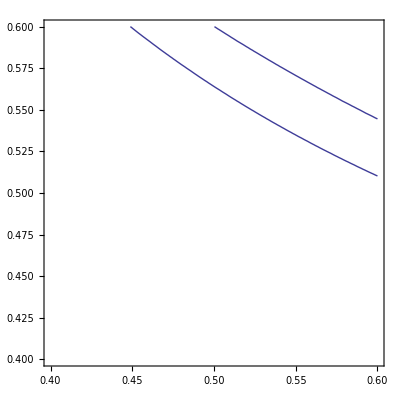

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2ns1s=ContourPlot[{chi2unionns[Ωm0,zt]==chi2minins[[1]]+2.30},{Ωm0,0.3,0.6},{zt,0.4,0.8}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2ns1sFF=FullForm[conchi2ns1s];
Export["OUTPUT\\2\\conchi2ns1sFF.dat",conchi2ns1sFF]
Export["OUTPUT\\2\\conchi2ns1s.eps",conchi2ns1s]
```

OUTPUT\2\conchi2ns1sFF.dat

OUTPUT\2\conchi2ns1s.eps

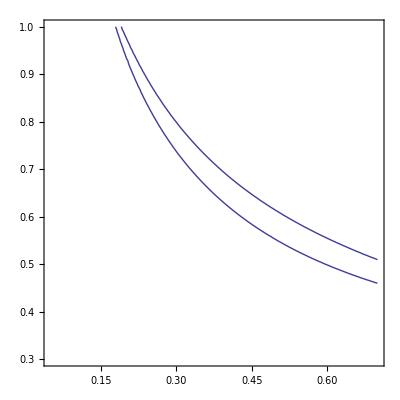

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2ns2s=ContourPlot[{chi2unionns[Ωm0,zt]==chi2minins[[1]]+6.18},{Ωm0,0.05,0.7},{zt,0.3,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2ns2sFF=FullForm[conchi2ns2s];
Export["OUTPUT\\2\\conchi2ns2sFF.dat",conchi2ns2sFF]
Export["OUTPUT\\2\\conchi2ns2s.eps",conchi2ns2s]
```

OUTPUT\2\conchi2ns2sFF.dat

OUTPUT\2\conchi2ns2s.eps

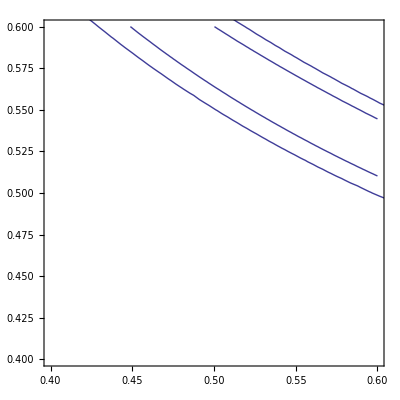

```mathematica
conchi2ns=Show[conchi2ns1s,conchi2ns2s]
```

```mathematica
conchi2nsFF=FullForm[conchi2ns];
Export["OUTPUT\\2\\conchi2nsFF.dat",conchi2nsFF]
Export["OUTPUT\\2\\conchi2ns.eps",conchins2]
```

OUTPUT\2\conchi2nsFF.dat

OUTPUT\2\conchi2ns.eps

#### With Systematic in data. Find the minimum of chi2.

```mathematica
Off[FindMinimum::lstol]
chi2mini=FindMinimum[chi2union[x,y],{x,0.15},{y,0.4}]
On[FindMinimum::lstol]
```

{530.353,{x→0.601866,y→0.524569}}

```mathematica
Export["OUTPUT\\2\\chi2union_minimum.dat",chi2mini]
```

OUTPUT\2\chi2union_minimum.dat

Plot the contour with confidential level 1σ and 2σ. This is a 2 parameter model. Δχ^2(1σ)=2.30 && Δχ^2(2σ)=6.18 && Δχ^2(3σ)=11.83.

With sys.

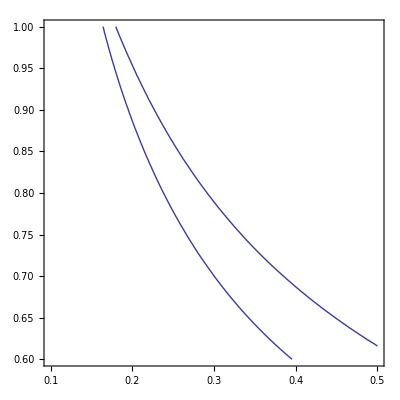

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi21s=ContourPlot[{chi2union[Ωm0,zt]==chi2mini[[1]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

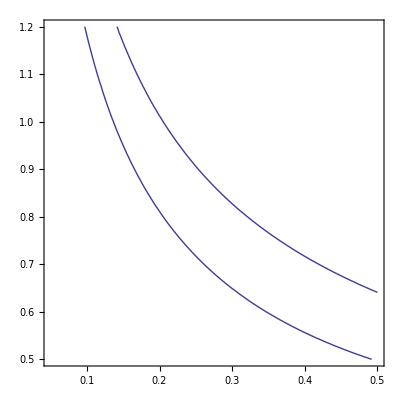

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi22s=ContourPlot[{chi2union[Ωm0,zt]==chi2mini[[1]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

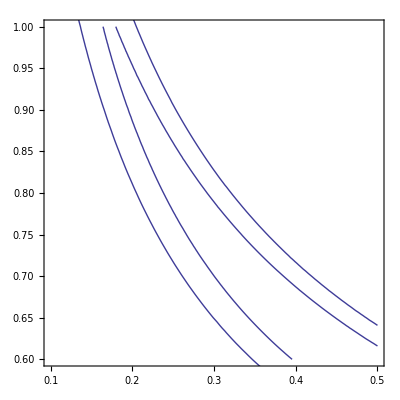

```mathematica
conchi2=Show[conchi21s,conchi22s]
```

```mathematica
Export["OUTPUT\\2\\conchi21s.eps",conchi21s]
Export["OUTPUT\\2\\conchi22s.eps",conchi22s]
Export["OUTPUT\\2\\conchi2.eps",conchi2]
```

OUTPUT\2\conchi21s.eps

OUTPUT\2\conchi22s.eps

OUTPUT\2\conchi2.eps

#### With only error, not the covariance matrix.

```mathematica
chi2minisl=FindMinimum[chi2unionsl[x,y],{x,0.15},{y,0.4}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{546.169,{x→0.587723,y→0.533675}}

```mathematica
chi2unionsl[0.3,0.729]
```

554.376

```mathematica
Export["OUTPUT\\2\\chi2unionsl_nimimum.dat",chi2minisl]
```

OUTPUT\2\chi2unionsl_nimimum.dat

Only error data.

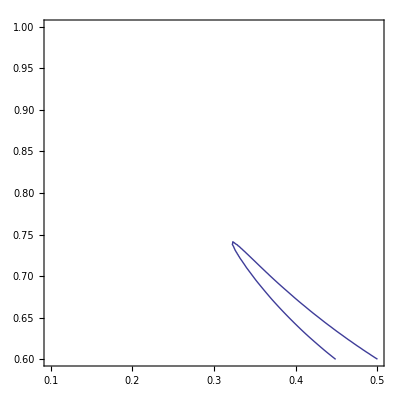

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2sl1s=ContourPlot[{chi2unionsl[Ωm0,zt]==chi2minisl[[1]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2sl1sFF=FullForm[conchi2sl1s];
Export["OUTPUT\\2\\conchi2sl1sFF.dat",conchi2sl1sFF]
Export["OUTPUT\\2\\conchi2sl1s.eps",conchi2sl1s]
```

OUTPUT\2\conchi2sl1sFF.dat

OUTPUT\2\conchi2sl1s.eps

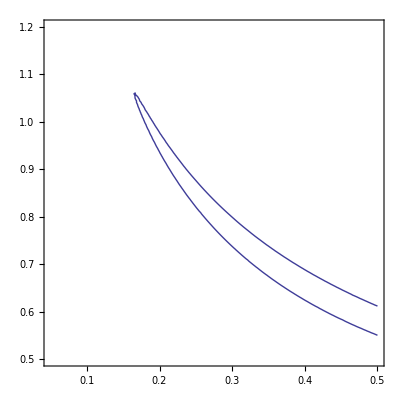

```mathematica
Off[NIntegrate::nlim]
Off[NIntegrate::slwcon]
conchi2sl2s=ContourPlot[{chi2unionsl[Ωm0,zt]==chi2minisl[[1]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::nlim]
On[NIntegrate::slwcon]
```

```mathematica
conchi2sl2sFF=FullForm[conchi2sl2s];
Export["OUTPUT\\2\\conchi2sl2sFF.dat",conchi2sl2sFF]
Export["OUTPUT\\2\\conchi2sl2s.eps",conchi2sl2s]
```

OUTPUT\2\conchi2sl2sFF.dat

OUTPUT\2\conchi2sl2s.eps

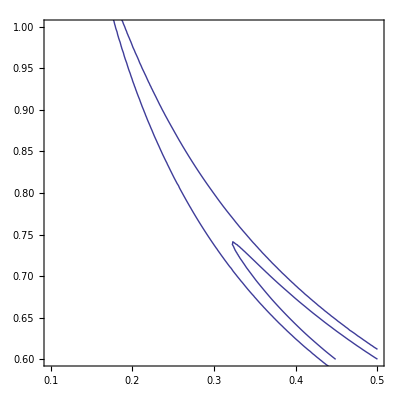

```mathematica
conchi2sl=Show[conchi2sl1s,conchi2sl2s]
```

```mathematica
Export["OUTPUT\\2\\conchi2slFF.dat",conchi2slFF]
Export["OUTPUT\\2\\conchi2sl.eps",conchi2sl]
```

OUTPUT\2\conchi2slFF.dat

OUTPUT\2\conchi2sl.eps

### Perform a grid method

It is unlucky that findminimum doesn’t work. SO I have to use grid method or Monte Carlo method. First try grid method.

The first try was exported to save for future use. Its “OUTPUT \\ 1\\ chi2_table _ 0.15-0.45_ 0.6-0.9.dat”.

A local view of the calculated chi2 data. As you see, the minimum is really hard to distingush. So I decide to write another method to do the calcualtions.

```mathematica
chi2tabtt=Import["OUTPUT\\1\\chi2_table_0.15-0.45_0.6-0.9.dat"];
```

```mathematica
ListPlot3D[chi2tabtt]
```

-Graphics3D-

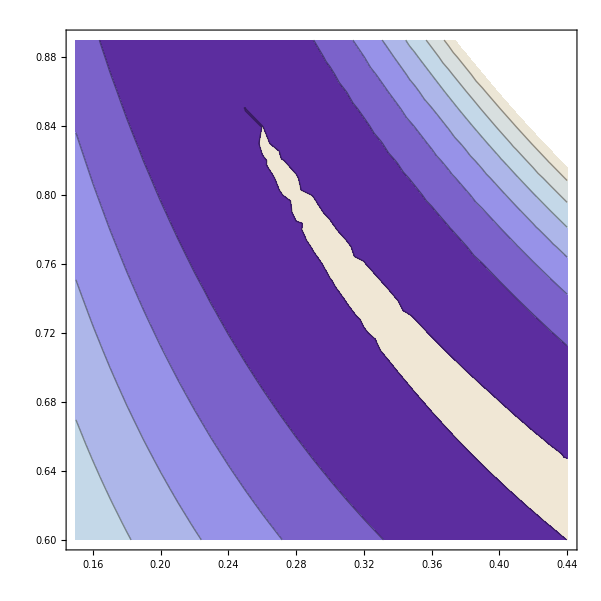

```mathematica
ListContourPlot[chi2tabtt,InterpolationOrder->1]
```

#### Calculate Contour and extract data from contour. Using data extracted from this GRIDING.

Use the data calculated before to determine the minimum of chi2.

```mathematica
chi2data1=Import["OUTPUT\\1\\chi2_table_0.15-0.45_0.6-0.9.dat","Table"];
```

Calculate the length of this table.

```mathematica
lenchi2data1=Length[chi2data1];
```

Reconstruct the table for use of find out the min.

```mathematica
chi2data1chi2=Table[chi2data1[[i]][[3]],{i,1,lenchi2data1}];
```

```mathematica
Min[chi2data1chi2]
```

546.96

Find out at which point chi2 becomes minimum.

```mathematica
chi2min=Select[chi2data1,#[[3]]<546.97&][[1]]
```

{0.44,0.62,546.96}

Plot the contour with confidential level 1σ and 2σ. This is a 2 parameter model. Δχ^2(1σ)=2.30 && Δχ^2(2σ)=6.18 && Δχ^2(3σ)=11.83.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.0159 and 9.81579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975752 and 0.76398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924283 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.0159 and 9.81579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975752 and 0.76398 for the integral and error estimates.

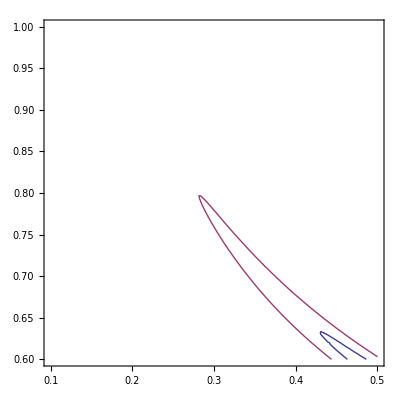

```mathematica
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30},{Ωm0,0.1,0.5},{zt,0.6,1.0}]
On[NIntegrate::nlim]
```

```mathematica
Off[NIntegrate::slwcon]
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30,chi2union[Ωm0,zt]==chi2min[[3]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::slwcon]
On[NIntegrate::nlim]
```

```mathematica
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30,chi2union[Ωm0,zt]==chi2min[[3]]+6.18},{Ωm0,0.05,0.5},{zt,0.5,1.2}]
On[NIntegrate::nlim]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999392671200132}. NIntegrate obtained 0.268826 and 0.0924286 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.996594340002196}. NIntegrate obtained 0.169935 and 0.0126272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00194}. NIntegrate obtained 10.2448 and 10.0447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {1.00072}. NIntegrate obtained 0.221815 and 0.0104377 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {0.999741179329708}. NIntegrate obtained 0.975972 and 0.764197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
Off[NIntegrate::nlim]
ContourPlot[{chi2union[Ωm0,zt]==chi2min[[3]],chi2union[Ωm0,zt]==chi2min[[3]]+2.30,chi2union[Ωm0,zt]==chi2min[[3]]+6.18,chi2union[Ωm0,zt]==chi2min[[3]]+11.83},{Ωm0,0,0.7},{zt,0.4,1.4}]
On[NIntegrate::nlim]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{546.169,{x→0.587723,y→0.533675}}